```mathematica
Guy F. Mongelli;
J. Adin Mann;
ECHE 475;
10/7/2012;
```

```mathematica
Assignment #2;
```

```mathematica
Key Manipulate Uses: Searching for Eigenvalues of a Matrix, Matrix Exponentiation, Exploration of Tensor Spaces, Determination of Solutions to coupled differential equations as a function of leading constants.
```

```mathematica
Problem1:
```

```mathematica
Part A:
```

```mathematica
let a and b be defined as:
```

```mathematica
a={a1,a2};
```

```mathematica
b={b1,b2};
```

```mathematica
Dot[a,b]
```

a1 b1+a2 b2

```mathematica
Apparently, there is a Norm[] function; which could have been used in the last problem of assignment #1 instead of utilizing it's definition.
```

```mathematica
Norm[a]
```

√(Abs[a1]^2+Abs[a2]^2)

```mathematica
Norm[b]
```

√(Abs[b1]^2+Abs[b2]^2)

```mathematica
Simplify[Norm[a]*Norm[b]]
```

√((Abs[a1]^2+Abs[a2]^2) (Abs[b1]^2+Abs[b2]^2))

```mathematica
FullSimplify[Norm[a]*Norm[b]]
```

√((Abs[a1]^2+Abs[a2]^2) (Abs[b1]^2+Abs[b2]^2))

```mathematica
This problem is getting at the vectoral definition of a and b and their relationship to the dot product.  The Magnitude or the Norm of the vector a or b is computed as the square root of the vector with it's complex conjugate.  It is important to note that this definition is explicitly the positive square root.  The multiplication of the real parts (both vectors a and b contain elements that are real) creates a non-negative real number.  The suare root of which is real and non-negative.  Since a and b are not colinear, there is a Cosine function (of the angle between a and b) relationship between the dot product (inner product) and the scalar product of the norm of a and the norm of b.  The Cosine may introduce a value between negative 1 and positive 1.  and is at maximum one.  Therefore the upper bound on the dot product of a and b is the product of the norms of A and B.
```

```mathematica
Part B;
```

```mathematica
Let the matrix An be defined as:
```

```mathematica
A[n_]=MatrixForm[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]
```

((1+n)/n | Log[n/(1+n)]
(-1)^n/n | -ⅇ^(-1/n))

```mathematica
The eigenvalues are given by:
```

```mathematica
MatrixForm[Eigenvalues[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]]
```

((ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n-√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n)
(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n+√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n))

```mathematica
Then the simplify command is applied:
```

```mathematica
MatrixForm[Simplify[Eigenvalues[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]]]
```

((ⅇ^(-1/n) (-n+ⅇ^(1/n) (1+n)-√((n+ⅇ^(1/n) (1+n))^2+4 (-1)^n ⅇ^(2/n) n Log[n/(1+n)])))/(2 n)
(ⅇ^(-1/n) (-n+ⅇ^(1/n) (1+n)+√((n+ⅇ^(1/n) (1+n))^2+4 (-1)^n ⅇ^(2/n) n Log[n/(1+n)])))/(2 n))

```mathematica
Then the FullSimplify command is applied. Alternatively, the determinant of A-lambda*I could have been computed and the roots of the characteristic polynomial factored out.
```

```mathematica
MatrixForm[FullSimplify[Eigenvalues[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]]]
```

((ⅇ^(-1/n) (-n+ⅇ^(1/n) (1+n)-√((n+ⅇ^(1/n) (1+n))^2+4 (-1)^n ⅇ^(2/n) n Log[n/(1+n)])))/(2 n)
(ⅇ^(-1/n) (-n+ⅇ^(1/n) (1+n)+√((n+ⅇ^(1/n) (1+n))^2+4 (-1)^n ⅇ^(2/n) n Log[n/(1+n)])))/(2 n))

```mathematica
In the positive infinite limit, the eigenvectors simplify to:
```

```mathematica
Limit[({{(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n-√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n)}, {(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n+√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n)}}),n->∞]
```

{-1,1}

```mathematica
The eigenvectors are given by the following matrix:
```

```mathematica
MatrixForm[Eigenvectors[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]]
```

(-(-1)^-n n (-ⅇ^(-1/n)-(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n-√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n)) | 1
-(-1)^-n n (-ⅇ^(-1/n)-(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n+√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n)) | 1)

```mathematica
MatrixForm[FullSimplify[Eigenvectors[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]]]
```

(1/2 (-1)^-n ⅇ^(-1/n) (n+ⅇ^(1/n) (1+n)-√((n+ⅇ^(1/n) (1+n))^2+4 (-1)^n ⅇ^(2/n) n Log[n/(1+n)])) | 1
1/2 (-1)^-n ⅇ^(-1/n) (n+ⅇ^(1/n) (1+n)+√((n+ⅇ^(1/n) (1+n))^2+4 (-1)^n ⅇ^(2/n) n Log[n/(1+n)])) | 1)

```mathematica
The inverse of A[n] is evaluated:
```

```mathematica
MatrixForm[Simplify[Inverse[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]]]
```

(n/(1+n+(-1)^n ⅇ^(1/n) Log[n/(1+n)]) | (ⅇ^(1/n) n Log[n/(1+n)])/(1+n+(-1)^n ⅇ^(1/n) Log[n/(1+n)])
((-1)^n ⅇ^(1/n))/(1+n+(-1)^n ⅇ^(1/n) Log[n/(1+n)]) | -(ⅇ^(1/n) (1+n))/(1+n+(-1)^n ⅇ^(1/n) Log[n/(1+n)]))

```mathematica
Then simplified:
```

```mathematica
MatrixForm[FullSimplify[Inverse[({{(n+1)/n, Log[n/(n+1)]}, {(-1)^n/n, -ⅇ^(-(1/n))}})]]]
```

(n/(1+n+(-1)^n ⅇ^(1/n) Log[n/(1+n)]) | n/((-1)^n+(ⅇ^(-1/n) (1+n))/(Log[n]-Log[1+n]))
1/((-1)^-n ⅇ^(-1/n) (1+n)+Log[n]-Log[1+n]) | -(ⅇ^(1/n) (1+n))/(1+n+(-1)^n ⅇ^(1/n) Log[n/(1+n)]))

```mathematica
It is clear why 0 and -1 have been excluded from the domain of An.  The former causes issues when evalueated in the first , third and fourth elements of the matrix due to denominator issues.  The latter has issues in the second element of the matrix (position Subscript[A, 1,2]).
```

```mathematica
To get a sense of the behavior of each of these functions, they are plotted:
```

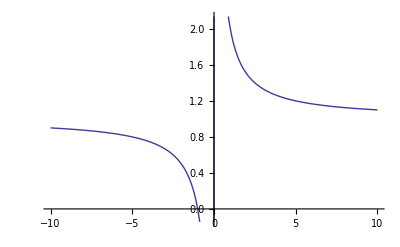

```mathematica
Plot[(1+n)/n,{n,-10,10}]
```

```mathematica
Limit[(1+n)/n,n->∞]
```

1

```mathematica
Limit[(1+n)/n,n->-∞]
```

1

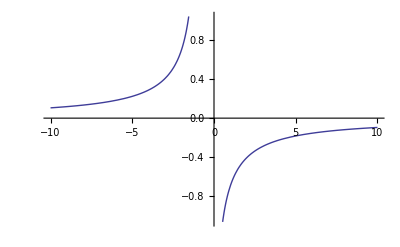

```mathematica
Plot[Log[n/(1+n)],{n,-10,10}]
```

```mathematica
Limit[Log[n/(1+n)],n->∞]
```

0

```mathematica
Limit[Log[n/(1+n)],n->-∞]
```

0

```mathematica
There is an issue with plotting the third element of the matrix in Mathematica.  to address this, both the positive and negative parts are evaluated, with the consideration that the true function will be alternating between points on these curves.  The function appeares to converge in both its positive and negative counterparts in both extreme limits.
```

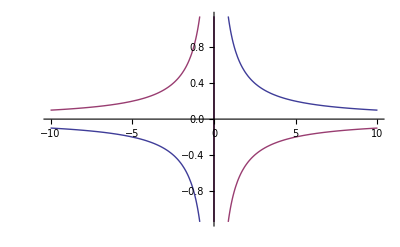

```mathematica
Plot[{1/n,-1/n},{n,-10,10},PlotRange->Automatic]
```

```mathematica
Limit[1/n,n->∞]
```

0

```mathematica
Limit[1/n,n->-∞]
```

0

```mathematica
Limit[-1/n,n->∞]
```

0

```mathematica
Limit[-1/n,n->-∞]
```

0

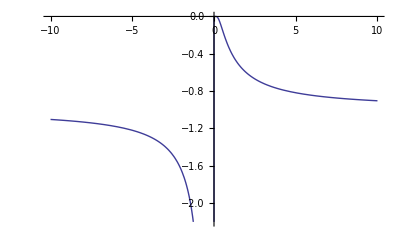

```mathematica
Plot[-ⅇ^(-1/n),{n,-10,10},PlotRange->Automatic]
```

```mathematica
Limit[-ⅇ^(-1/n),n->∞]
```

-1

```mathematica
Limit[-ⅇ^(-1/n),n->-∞]
```

-1

```mathematica
Mathematica does not perform the Limit of each element of a metrix readily.
```

```mathematica
Limit[A[n],n->∞]
```

Limit[((1+n)/n | Log[n/(1+n)]
(-1)^n/n | -ⅇ^(-1/n)),n→∞]

```mathematica
So the limit of A[n] will be evaluated as the limit of each element.  The Limit of A[n] as n goes to infiniti is:
```

```mathematica
({{1, 0}, {0, -1}})
```

```mathematica
The Limit of A[n] as n goes to negative infiniti is the same as the previous case:
```

```mathematica
({{1, 0}, {0, -1}})
```

```mathematica
Part C:
```

```mathematica
B=A[n]
```

((1+n)/n | Log[n/(1+n)]
(-1)^n/n | -ⅇ^(-1/n))

```mathematica
Eigenvalues[B,n]
```

Eigenvalues[((1+n)/n | Log[n/(1+n)]
(-1)^n/n | -ⅇ^(-1/n)),n]

```mathematica
Find the determinant of An-λ*I, which gives the characteristic polynamial.
```

```mathematica
Det[({{(1+n)/n-λ, Log[n/(1+n)]}, {(-1)^n/n, -ⅇ^(-1/n)-λ}})]
```

-ⅇ^(-1/n)-ⅇ^(-1/n)/n-λ+ⅇ^(-1/n) λ-λ/n+λ^2-((-1)^n Log[n/(1+n)])/n

```mathematica
f[n_]=-ⅇ^(-1/n)-ⅇ^(-1/n)/n-λ+ⅇ^(-1/n) λ-λ/n+λ^2-((-1)^n Log[n/(1+n)])/n
```

-ⅇ^(-1/n)-ⅇ^(-1/n)/n-λ+ⅇ^(-1/n) λ-λ/n+λ^2-((-1)^n Log[n/(1+n)])/n

```mathematica
Then find value of this determinant as n goes to ∞.
```

```mathematica
Limit[f[n],n->∞]
```

-1+λ^2

```mathematica
Then, determine the solutions to this characteristic polynomial.
```

```mathematica
Solve[-1+λ^2==0,λ]
```

{{λ→-1},{λ→1}}

```mathematica
For the General Case of arbitrary n:
```

```mathematica
Eigen[n_]=Solve[f[n] == 0, λ]
```

{{λ→(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n-√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n)},{λ→(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n+√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n)}}

```mathematica
Eigen[2]
```

{{λ→(-2+3 √ⅇ-√((2-3 √ⅇ)^2-8 √ⅇ (-3+√ⅇ Log[3/2])))/(4 √ⅇ)},{λ→(-2+3 √ⅇ+√((2-3 √ⅇ)^2-8 √ⅇ (-3+√ⅇ Log[3/2])))/(4 √ⅇ)}}

```mathematica
Mathematica does not want to solve for the eigenvalues in the infinite limit in the following manner.
```

```mathematica
Limit[Eigen[n],n->∞]
```

{{Limit[λ→(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n-√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n),n→∞]},{Limit[λ→(ⅇ^(-1/n) (ⅇ^(1/n)-n+ⅇ^(1/n) n+√((-ⅇ^(1/n)+n-ⅇ^(1/n) n)^2-4 ⅇ^(1/n) n (-1-n-(-1)^n ⅇ^(1/n) Log[n/(1+n)]))))/(2 n),n→∞]}}

```mathematica
The following entry will compute the specific eigenvalues of arbitrary values of n, even when the roots are complex.
```

```mathematica
Manipulate[N[Eigen[l],3],{l,-1000,1000}]
```

```mathematica
MatrixForm[IdentityMatrix[2]]
```

(1 | 0
0 | 1)

```mathematica
Simplify[λ*MatrixForm[IdentityMatrix[2]]]
```

λ (1 | 0
0 | 1)

```mathematica
Mathematica then gives some erroneous responses when prompted in this form:
```

```mathematica
Det[A[n]-λ*IdentityMatrix[2]]
```

λ^2-2 λ ((1+n)/n | Log[n/(1+n)]
(-1)^n/n | -ⅇ^(-1/n))

```mathematica
Solve[Det[A[n]-λ*IdentityMatrix[2]]==0,λ]
```

{{λ→0},{λ→2 ((1+n)/n | Log[n/(1+n)]
(-1)^n/n | -ⅇ^(-1/n))}}

```mathematica
Problem2:
```

```mathematica
This problem is alluding to a useful method to solve ordinary differential equations.It is important to note that not all matrices are diagnalizeable.  If the eigenvector matrix is not invertible, then the matrix is not diagnalizable.
```

```mathematica
Part A:
```

```mathematica
First create several symmetric matrices of various sizes:
```

```mathematica
MatrixForm[UpperTriangularize[({{x11, x22}, {x22, x11}})]]
```

(x11 | x22
0 | x11)

```mathematica
MatrixForm[({{x11, x22}, {x22, x11}})]
```

(x11 | x22
x22 | x11)

```mathematica
This is the diagnalized, row-reduced  echelon form of the matrix.
```

```mathematica
MatrixForm[RowReduce[({{x11, x22}, {x22, x11}})]]
```

(1 | 0
0 | 1)

```mathematica
The following line of code tests to see if a matrix is symmetric or not.
```

```mathematica
SymmetricMatrixQ[({{x11, x22}, {x22, x11}})]
```

True

```mathematica
For any n by n matrix, the test of diagnalizability is if there are n discrete eigenvalues.  Since there are 2 eigenvalues for this 2 by 2 matrix, it is diagnalizable. Diagnalized matrices are useful in constructing the powers of a matrix.
```

```mathematica
MatrixForm[Eigenvalues[({{x11, x22}, {x22, x11}})]]
```

(x11-x22
x11+x22)

```mathematica
Det[({{x11, x22}, {x22, x11}})]
```

x11^2-x22^2

```mathematica
MatrixForm[Eigenvectors[({{x11, x22}, {x22, x11}})]]
```

(-1 | 1
1 | 1)

```mathematica
Det[({{-1, 1}, {1, 1}})]
```

-2

```mathematica
MatrixForm[Transpose[Eigenvectors[({{x11, x22}, {x22, x11}})]]]
```

(-1 | 1
1 | 1)

```mathematica
MatrixForm[Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]]]
```

(-1/2 | 1/2
1/2 | 1/2)

```mathematica
({{-1/2, 1/2}, {1/2, 1/2}})({{-1, 1}, {1, 1}})
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
MatrixForm[Inverse[Transpose[Eigenvectors[({{x11, x22}, {x22, x11}})]]]]
```

(-1/2 | 1/2
1/2 | 1/2)

```mathematica
Det[({{-1/2, 1/2}, {1/2, 1/2}})]
```

-1/2

```mathematica
MatrixForm[Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]].({{x11, x22}, {x22, x11}}).Eigenvectors[({{x11, x22}, {x22, x11}})]]
```

(x11-x22 | 0
0 | x11+x22)

```mathematica
CharacteristicPolynomial[({{x11, x22}, {x22, x11}}),λ]
```

x11^2-x22^2-2 x11 λ+λ^2

```mathematica
Roots[x11^2-x22^2-2 x11 λ+λ^2==0,λ]
```

λ==x11+x22||λ==x11-x22

```mathematica
Mathematica will produce the eigenvalues and eigenvectors simultaneously with the eigensystem command:
```

```mathematica
Eigensystem[{{x11, x22}, {x22, x11}}]
```

{{x11-x22,x11+x22},{{-1,1},{1,1}}}

```mathematica
In order to do proper Matrix Multiplication, the '*' should not be used.  Instead a lowercase . is used to denote matrix products.
```

```mathematica
MatrixForm[Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]]*Eigenvectors[({{x11, x22}, {x22, x11}})]]
```

```mathematica
The value of the following matrix shoule be the Identity matrix.
```

```mathematica
MatrixForm[Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]].Eigenvectors[({{x11, x22}, {x22, x11}})]]
```

(1 | 0
0 | 1)

```mathematica
This should also be the identity matrix:
```

```mathematica
MatrixForm[Eigenvectors[({{x11, x22}, {x22, x11}})].Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]]]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[Eigenvectors[({{x11, x22}, {x22, x11}})].({{x11, x22}, {x22, x11}}).Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]]]
```

(x11-x22 | (x11-x22)/2+1/2 (-x11+x22)
1/2 (-x11-x22)+(x11+x22)/2 | x11+x22)

```mathematica
MatrixForm[({{-1, 1}, {1, 1}}).({{x11, x22}, {x22, x11}}).Inverse[({{-1, 1}, {1, 1}})]]
```

(x11-x22 | (x11-x22)/2+1/2 (-x11+x22)
1/2 (-x11-x22)+(x11+x22)/2 | x11+x22)

```mathematica
MatrixForm[Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]].({{x11, x22}, {x22, x11}}).Eigenvectors[({{x11, x22}, {x22, x11}})]]
```

(x11-x22 | 0
0 | x11+x22)

```mathematica
MatrixForm[Inverse[Transpose[Eigenvectors[({{x11, x22}, {x22, x11}})]]].({{x11, x22}, {x22, x11}}).Transpose[Eigenvectors[({{x11, x22}, {x22, x11}})]]]
```

(x11-x22 | 0
0 | x11+x22)

```mathematica
MatrixForm[Eigenvectors[({{x11, x22}, {x22, x11}})].({{x11, x22}, {x22, x11}}).Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]]]
```

(x11-x22 | (x11-x22)/2+1/2 (-x11+x22)
1/2 (-x11-x22)+(x11+x22)/2 | x11+x22)

```mathematica
This calculates the form of the matrix that will assist in diagonalizing the symmetrix matrix.
```

```mathematica
MatrixForm[Inverse[{{x11, x22}, {x22, x11}}]*({{1, 0}, {0, 1}})]
```

(x11/(x11^2-x22^2) | 0
0 | x11/(x11^2-x22^2))

```mathematica
The next two cells look at how Mathematica treats matrices and exponents.
```

```mathematica
({{x11, x22}, {x22, x11}})^2
```

{{x11^2,x22^2},{x22^2,x11^2}}

```mathematica
MatrixPower[({{x11, x22}, {x22, x11}}),2]
```

{{x11^2+x22^2,2 x11 x22},{2 x11 x22,x11^2+x22^2}}

```mathematica
The above expressions are not in agreement and the second definition holds true to defining the matrix power as multiplication of a matrix by itself.  The former looks at each element to a certain power, which is incorrect in the contexts of our course.
```

```mathematica
The next bit of code computes the patial sum that approximates the exponential of a matrix.   It is incorrect because it is simply raising each element to the power of k instead of performing matrix
```

```mathematica
Manipulate[MatrixForm[∑_(k=0)^L 1/(k!)({{x11, x22}, {x22, x11}})^k],{L,1,2,3,4,5,6,7,8,9,10}]
```

```mathematica
Manipulate[MatrixForm[∑_(k=0)^L 1/(k!)MatrixPower[({{x11, x22}, {x22, x11}}),k]],{L,1,2,3,4,5,6,7,8,9,10}]
```

```mathematica
Manipulate[MatrixForm[FullSimplify[∑_(k=0)^L 1/(k!)MatrixPower[({{x11, x22}, {x22, x11}}),k]]],{L,1,2,3,4,5,6,7,8,9,10}]
```

```mathematica
Manipulate[MatrixForm[Expand[∑_(k=0)^L 1/(k!)MatrixPower[({{x11, x22}, {x22, x11}}),k]]],{L,1,2,3,4,5,6,7,8,9,10}]
```

```mathematica
Based upon our discussion after lecture, this is not the correct form:
```

```mathematica
MatrixForm[∑_(k=0)^∞ 1/(k!)({{x11, x22}, {x22, x11}})^k]
```

(ⅇ^x11 | ⅇ^x22
ⅇ^x22 | ⅇ^x11)

```mathematica
This computes the exponential as an approximation to term L using the correct definition of the raising of a matrix to a power:
```

```mathematica
MatrixForm[∑_(k=0)^L 1/(k!)MatrixPower[({{x11, x22}, {x22, x11}}),k]]
```

((ⅇ^(x11-x22) (Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L]) | (ⅇ^(x11-x22) (-Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L])
(ⅇ^(x11-x22) (-Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L]) | (ⅇ^(x11-x22) (Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L]))

```mathematica
It is important to note that the inverse of a matrix may be computed by evaluation of: ∑_(n=1)^∞ (I-A)^n
```

```mathematica
The exponential term to infiniti is the exact definition:
```

```mathematica
MatrixForm[∑_(k=0)^∞ 1/(k!)MatrixPower[({{x11, x22}, {x22, x11}}),k]]
```

(1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22)) | 1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22))
1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22)) | 1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22)))

```mathematica
Needs["Combinatorica`"];
```

```mathematica
SymmetricQ[({{1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22)), 1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22))}, {1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22)), 1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22))}})]
```

True

```mathematica
The exponential of the matrix is a symmetrix matrix.  Furthermore, it is diagnalized by the same transformation as the original matrix.
```

```mathematica
MatrixForm[Inverse[Eigenvectors[({{x11, x22}, {x22, x11}})]].({{1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22)), 1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22))}, {1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22)), 1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22))}}).Eigenvectors[({{x11, x22}, {x22, x11}})]]
```

(-1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22))+1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22)) | 0
0 | 1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22))+1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22)))

```mathematica
To get a better understanding of each of the matrix elements, they are plotted below as a function of x11.  The manipulate command allows for the exploration of x22 space.
```

```mathematica
Manipulate[Plot[{1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22)),1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22)),1/2 ⅇ^(x11-x22) (-1+ⅇ^(2 x22)),1/2 ⅇ^(x11-x22) (1+ⅇ^(2 x22))},{x11,-10,10}],{x22,-10,10}]
```

```mathematica
Application of the diagnalization matrix to the infinite sum exponential:
```

```mathematica
MatrixForm[FullSimplify[({{x11/(x11^2-x22^2), 0}, {0, x11/(x11^2-x22^2)}})({{(ⅇ^(x11-x22) (Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L]), (ⅇ^(x11-x22) (-Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L])}, {(ⅇ^(x11-x22) (-Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L]), (ⅇ^(x11-x22) (Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 Gamma[1+L])}})]]
```

((ⅇ^(x11-x22) x11 (Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 (x11^2-x22^2) Gamma[1+L]) | 0
0 | (ⅇ^(x11-x22) x11 (Gamma[1+L,x11-x22]+ⅇ^(2 x22) Gamma[1+L,x11+x22]))/(2 (x11^2-x22^2) Gamma[1+L]))

```mathematica
The matrix is also diagnalized.
```

```mathematica
For the 3 by 3 case:
```

```mathematica
{{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}
```

```mathematica
SymmetricMatrixQ[{{z11, z12, z13, z14}, {z12, z22, z23, z42}, {z13, z23, z33, z43}, {z14, z42, z43, z44}}]
```

True

```mathematica
MatrixForm[RowReduce[{{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
The following two cells do not give a result within approxamately 15 minutes time.
```

```mathematica
MatrixForm[∑_(k=0)^L 1/(k!)MatrixPower[({{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}),k]]
```

$Aborted

```mathematica
MatrixForm[∑_(k=0)^∞ 1/(k!)MatrixPower[({{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}),k]]
```

$Aborted

```mathematica
SymmetricMatrixQ[{{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}]
```

True

```mathematica
FullSimplify[Det[{{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}]]
```

-y13^2 y22+2 y12 y13 y23-y11 y23^2-y12^2 y33+y11 y22 y33

```mathematica
Eigenvalues[{{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}]
```

{Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,1],Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,2],Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,3]}

```mathematica
I'm not certain what the # symbol means in this context.  Is it 1)the cardinality of the set (set theory)2) connected sum (manifold theory)3) primorial of the set 4)simmilar to the wedge operator.
```

```mathematica
In the following command, Mathematica is not natively solving for the roots of the cubic functions in the general case.
```

```mathematica
MatrixForm[Eigenvectors[{{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}]]
```

(-(y33-Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,1])/y13+(y23 (-y13 y23+y12 y33-y12 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,1]))/(y13 (-y13 y22+y12 y23+y13 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,1])) | -(-y13 y23+y12 y33-y12 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,1])/(-y13 y22+y12 y23+y13 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,1]) | 1
-(y33-Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,2])/y13+(y23 (-y13 y23+y12 y33-y12 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,2]))/(y13 (-y13 y22+y12 y23+y13 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,2])) | -(-y13 y23+y12 y33-y12 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,2])/(-y13 y22+y12 y23+y13 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,2]) | 1
-(y33-Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,3])/y13+(y23 (-y13 y23+y12 y33-y12 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,3]))/(y13 (-y13 y22+y12 y23+y13 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,3])) | -(-y13 y23+y12 y33-y12 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,3])/(-y13 y22+y12 y23+y13 Root[y13^2 y22-2 y12 y13 y23+y11 y23^2+y12^2 y33-y11 y22 y33+(-y12^2-y13^2+y11 y22-y23^2+y11 y33+y22 y33) #1+(-y11-y22-y33) #1^2+#1^3&,3]) | 1)

```mathematica
Inverse[%].{{y11, y12, y13}, {y12, y22, y23}, {y13, y23, y33}}.%
```

```mathematica
The case of the 4by 4 matrix is not completely worked out.
```

```mathematica
For the case of a 4by4 matrix:
```

```mathematica
{{z11, z12, z13, z14}, {z12, z22, z23, z42}, {z13, z23, z33, z43}, {z14, z42, z43, z44}}
```

```mathematica
MatrixForm[RowReduce[{{z11, z12, z13, z14}, {z12, z22, z23, z42}, {z13, z23, z33, z43}, {z14, z42, z43, z44}}]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MatrixForm[Inverse[{{z11, z12, z13, z14}, {z12, z22, z23, z42}, {z13, z23, z33, z43}, {z14, z42, z43, z44}}]*({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})]
```

((-z33 z42^2+2 z23 z42 z43-z22 z43^2-z23^2 z44+z22 z33 z44)/(z14^2 z23^2-z14^2 z22 z33-2 z13 z14 z23 z42+2 z12 z14 z33 z42+z13^2 z42^2-z11 z33 z42^2+2 z13 z14 z22 z43-2 z12 z14 z23 z43-2 z12 z13 z42 z43+2 z11 z23 z42 z43+z12^2 z43^2-z11 z22 z43^2-z13^2 z22 z44+2 z12 z13 z23 z44-z11 z23^2 z44-z12^2 z33 z44+z11 z22 z33 z44) | 0 | 0 | 0
0 | (-z14^2 z33+2 z13 z14 z43-z11 z43^2-z13^2 z44+z11 z33 z44)/(z14^2 z23^2-z14^2 z22 z33-2 z13 z14 z23 z42+2 z12 z14 z33 z42+z13^2 z42^2-z11 z33 z42^2+2 z13 z14 z22 z43-2 z12 z14 z23 z43-2 z12 z13 z42 z43+2 z11 z23 z42 z43+z12^2 z43^2-z11 z22 z43^2-z13^2 z22 z44+2 z12 z13 z23 z44-z11 z23^2 z44-z12^2 z33 z44+z11 z22 z33 z44) | 0 | 0
0 | 0 | (-z14^2 z22+2 z12 z14 z42-z11 z42^2-z12^2 z44+z11 z22 z44)/(z14^2 z23^2-z14^2 z22 z33-2 z13 z14 z23 z42+2 z12 z14 z33 z42+z13^2 z42^2-z11 z33 z42^2+2 z13 z14 z22 z43-2 z12 z14 z23 z43-2 z12 z13 z42 z43+2 z11 z23 z42 z43+z12^2 z43^2-z11 z22 z43^2-z13^2 z22 z44+2 z12 z13 z23 z44-z11 z23^2 z44-z12^2 z33 z44+z11 z22 z33 z44) | 0
0 | 0 | 0 | (-z13^2 z22+2 z12 z13 z23-z11 z23^2-z12^2 z33+z11 z22 z33)/(z14^2 z23^2-z14^2 z22 z33-2 z13 z14 z23 z42+2 z12 z14 z33 z42+z13^2 z42^2-z11 z33 z42^2+2 z13 z14 z22 z43-2 z12 z14 z23 z43-2 z12 z13 z42 z43+2 z11 z23 z42 z43+z12^2 z43^2-z11 z22 z43^2-z13^2 z22 z44+2 z12 z13 z23 z44-z11 z23^2 z44-z12^2 z33 z44+z11 z22 z33 z44))

```mathematica
Define the exponential of a matrix to be defined as:
```

```mathematica
ⅇ^X=∑_(k=0)^∞ 1/(k!)X^k
```

```mathematica
MatrixForm[∑_(k=0)^2 1/(k!)({{x11, x22}, {x22, x11}})^k]
```

(1+x11+x11^2/2 | 1+x22+x22^2/2
1+x22+x22^2/2 | 1+x11+x11^2/2)

```mathematica
∑_(k=0)^5 1/(k!)({{x11, x22}, {x22, x11}})^k
```

```mathematica
By this definition, the matrix resulting from the matrix exponential will depend on integer powers of X itself.  Since raising a matrix to any power will not change the dimensions of the matrix, the result will be an n by n matrix if the input matrix is an n by n matrix.  Without placing particular contraints on the matrix A, it does not appear that the exponential of a matrix will be necessarily symmetric for the general case.
```

```mathematica
Clear[a,b,c,d]
```

```mathematica
A matrix with random elements between 0 and 1.
```

```mathematica
MatrixForm[RandomReal[{0,1},{5,5}]]
```

(0.615139 | 0.718828 | 0.379799 | 0.928684 | 0.653989
0.194011 | 0.111739 | 0.270599 | 0.906822 | 0.897661
0.323529 | 0.141938 | 0.478566 | 0.107927 | 0.676909
0.920967 | 0.265063 | 0.00682614 | 0.400452 | 0.678514
0.863905 | 0.42073 | 0.223335 | 0.858904 | 0.810632)

```mathematica
P=MatrixForm[({{a, b}, {c, d}})]
```

(a | b
c | d)

```mathematica
MatrixPower[P,1/2]
```

MatrixPower[(a | b
c | d),1/2]

```mathematica
Q=MatrixForm[({{a, b, c}, {d, e, f}, {g, h, i}})]
```

(a | b | c
d | e | f
g | h | i)

```mathematica
MatrixPower[Q,1/2]
```

MatrixPower[(a | b | c
d | e | f
g | h | i),1/2]

```mathematica
R=MatrixForm[({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})]
```

(a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p)

```mathematica
MatrixPower[R,1/2]
```

MatrixPower[(a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p),1/2]

```mathematica
Part B: The method to define the square root of a matrix is to consdier a matrix that is multiplied by itself and equals a second matrix, then to determine what each element of the self-multiplied matrix must be in terms of the elements of the second matrix.  In Mathematica, this is performed readily with the MatrixPower[] function as well.  This is written for A as:
```

```mathematica
A=({{a, b}, {c, d}})
```

```mathematica
Trace[A]=a+d
```

```mathematica
Det[A]=a*d-b*c
```

```mathematica
Clear[a,b]
```

```mathematica
A^(1/2)=1/(±√(Trace[A]+2*Det[A]))({{a+Det[A], b}, {c, d+Det[A]}})
```

```mathematica
Vars1=1/(√((a+d)+2*(a*d-b*c)))
```

1/(√(a+d+2 (-b c+a d)))

```mathematica
Vars2=-1/(√((a+d)+2*(a*d-b*c)))
```

-1/(√(a+d+2 (-b c+a d)))

```mathematica
MatrixForm[Simplify[1/(√(Tr[({{a, b}, {c, d}})]+2*Det[({{a, b}, {c, d}})]))({{a+Sqrt[Det[({{a, b}, {c, d}})]], b}, {c, d+Sqrt[Det[({{a, b}, {c, d}})]]}})]]
```

((a+√(-b c+a d))/(√(a-2 b c+d+2 a d)) | b/(√(a-2 b c+d+2 a d))
c/(√(a-2 b c+d+2 a d)) | (d+√(-b c+a d))/(√(a-2 b c+d+2 a d)))

```mathematica
MatrixForm[MatrixPower[{{a, b}, {c, d}},(1/2)]]
```

((√(a+d-√(a^2+4 b c-2 a d+d^2)) (-a+d+√(a^2+4 b c-2 a d+d^2)))/(2 √2 √(a^2+4 b c-2 a d+d^2))-((-a+d-√(a^2+4 b c-2 a d+d^2)) √(a+d+√(a^2+4 b c-2 a d+d^2)))/(2 √2 √(a^2+4 b c-2 a d+d^2)) | -(√(a+d-√(a^2+4 b c-2 a d+d^2)) (a-d+√(a^2+4 b c-2 a d+d^2)) (-a+d+√(a^2+4 b c-2 a d+d^2)))/(4 √2 c √(a^2+4 b c-2 a d+d^2))-((-a+d-√(a^2+4 b c-2 a d+d^2)) (-a+d+√(a^2+4 b c-2 a d+d^2)) √(a+d+√(a^2+4 b c-2 a d+d^2)))/(4 √2 c √(a^2+4 b c-2 a d+d^2))
-(c √(a+d-√(a^2+4 b c-2 a d+d^2)))/(√2 √(a^2+4 b c-2 a d+d^2))+(c √(a+d+√(a^2+4 b c-2 a d+d^2)))/(√2 √(a^2+4 b c-2 a d+d^2)) | (√(a+d-√(a^2+4 b c-2 a d+d^2)) (a-d+√(a^2+4 b c-2 a d+d^2)))/(2 √2 √(a^2+4 b c-2 a d+d^2))+((-a+d+√(a^2+4 b c-2 a d+d^2)) √(a+d+√(a^2+4 b c-2 a d+d^2)))/(2 √2 √(a^2+4 b c-2 a d+d^2)))

```mathematica
This proves that the matrix in the above cell is the square root.
```

```mathematica
FullSimplify[MatrixPower[{{a, b}, {c, d}},(1/2)].MatrixPower[{{a, b}, {c, d}},(1/2)]]
```

{{a,b},{c,d}}

```mathematica
MatrixForm[Simplify[1/(√(Tr[({{a, b}, {c, d}})]+2*Det[({{a, b}, {c, d}})]))({{a+Det[({{a, b}, {c, d}})], b}, {c, d+Det[({{a, b}, {c, d}})]}})]]
```

((a-b c+a d)/(√(a-2 b c+d+2 a d)) | b/(√(a-2 b c+d+2 a d))
c/(√(a-2 b c+d+2 a d)) | (-b c+d+a d)/(√(a-2 b c+d+2 a d)))

```mathematica
FullSimplify[({{(a-b c+a d)/(√(a-2 b c+d+2 a d)), b/(√(a-2 b c+d+2 a d))}, {c/(√(a-2 b c+d+2 a d)), (-b c+d+a d)/(√(a-2 b c+d+2 a d))}}).({{(a-b c+a d)/(√(a-2 b c+d+2 a d)), b/(√(a-2 b c+d+2 a d))}, {c/(√(a-2 b c+d+2 a d)), (-b c+d+a d)/(√(a-2 b c+d+2 a d))}})]
```

{{(b c+(a-b c+a d)^2)/(a-2 b c+d+2 a d),b},{c,(b c+(-b c+d+a d)^2)/(a-2 b c+d+2 a d)}}

```mathematica
Problem3:
```

```mathematica
Consider a 2,3, and 4 'step' reaction systems.  Let the follwing matrix contain the k coefficients.
```

```mathematica
The first column corresponds to k1, the second to k2 and so on.
```

```mathematica
({{-1, 0, 0}, {1, -1, 0}, {0, 1, -1}})
```

{{-1,0,0},{1,-1,0},{0,1,-1}}

```mathematica
MatrixForm[RowReduce[({{-1, 0, 0}, {1, -1, 0}, {0, 1, -1}})]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Eigenvalues[({{-1, 0, 0}, {1, -1, 0}, {0, 1, -1}})]
```

{-1,-1,-1}

```mathematica
MatrixForm[Eigenvectors[({{-1, 0, 0}, {1, -1, 0}, {0, 1, -1}})]]
```

(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0)

```mathematica
Problem 3:
```

```mathematica
Part A :
```

```mathematica
INPUT:
```

```mathematica
x[L,0]=
```

```mathematica
FUNCTIONAL FORM:
```

```mathematica
(* I'll need to remove the m for i=r terms of the denominator will be zero *)
```

```mathematica
x[L_,t_]=∑_(i=1)^L x[L,0]*(∏_(r=i)^L k[r])∑_(r=i)^I Exp[-k[r]*t]/(∏_(m=i)^I (k[m]-k[r]))
```

```mathematica
One way to do this is two split the sum into two terms: one for the km less than kr and one for the terms of km  greater than kr
```

```mathematica
If there is a relationship between the k values then the distribution of the products will essentially sample the the rate function and determine the kinetics. (This is only if I set it up correctly).  If the rate constants are random, then this will give a different distribution of products.  Does the scale of the rate constants really matter (* 10^-14 *)
```

```mathematica
Rate constant units
```

```mathematica
0th order-mol/L/s
```

```mathematica
1st order- 1/s
```

```mathematica
2nd order-L/mol/s
```

```mathematica
3rd order-L^2/mol^2/s
```

```mathematica
(m+n)th order-mol^(1-m+n)*L^(m+n-1)*s^-1
```

```mathematica
There will be n rate constants and n+1 equations.
```

```mathematica
This system could be defined explicitly for each case of n equations.
```

```mathematica
(* system = {{x1'[t] == -k1*x1[t]}, {x2'[t] ==k1*x1[t]-k2*x2[t]}, {x3'[t] == -k[3]*x2[t]}}
```

{{x1'[t]==-k1 x1[t]},{x2'[t]==k1 x1[t]-k2 x2[t]},{x3'[t]==-x2[t]}}

```mathematica
Clear[k[n]]
```

Clear::ssym: k[n] is not a symbol or a string.

```mathematica
Mathematica will not solve the differential equations without determing the values of the constants.  Some interesting values are assumed here and then the solutions evaluated without matrix methods.
```

```mathematica
DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==1,x3[0]==1},{x1[t],x2[t],x3[t],k[1],k[2],k[3]},t]
```

DSolve::dsfun: Sinh[1] cannot be used as a function.

```mathematica
For x3[0]==1:
```

```mathematica
k[n_]=1
```

1

```mathematica
DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==1,x3[0]==1},{x1[t],x2[t],x3[t]},t]
```

{{x1[t]→ⅇ^-t,x2[t]→ⅇ^-t (1+t),x3[t]→-ⅇ^-t (-2+ⅇ^t-t)}}

```mathematica
k[n_]=Sin[n*Pi/2]
```

Sin[(n π)/2]

```mathematica
DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==1,x3[0]==1},{x1[t],x2[t],x3[t]},t]
```

{{x1[t]→ⅇ^-t,x2[t]→ⅇ^-t (-1+2 ⅇ^t),x3[t]→-ⅇ^-t (1-2 ⅇ^t+2 ⅇ^t t)}}

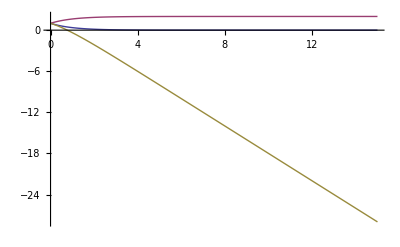

```mathematica
Plot[{ⅇ^-t,ⅇ^-t (-1+2 ⅇ^t),-ⅇ^-t (1-2 ⅇ^t+2 ⅇ^t t)},{t,0,15}]
```

```mathematica
Manipulate[DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==b,x3[0]==c},{x1[t],x2[t],x3[t]},t],{b,0,1},{c,0,1}]
```

```mathematica
k[n_]=Cos[n*Pi/2]
```

Cos[(n π)/2]

```mathematica
DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==1,x3[0]==1},{x1[t],x2[t],x3[t]},t]
```

{{x1[t]→1,x2[t]→ⅇ^t,x3[t]→2-ⅇ^t}}

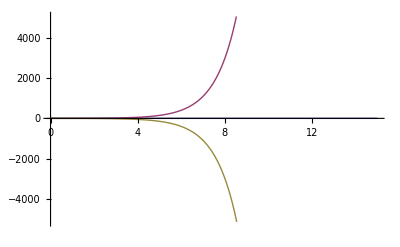

```mathematica
Plot[{1,ⅇ^t,2-ⅇ^t},{t,0,15}]
```

```mathematica
k[n_]=Gamma[n*Pi/2]
```

Gamma[(n π)/2]

```mathematica
DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==1,x3[0]==1},{x1[t],x2[t],x3[t]},t]
```

{{x1[t]→ⅇ^(-t Gamma[π/2]),x2[t]→(ⅇ^(-t Gamma[π/2]-t Gamma[π]) (-2 ⅇ^(t Gamma[π/2]) Gamma[π/2]+ⅇ^(t Gamma[π]) Gamma[π/2]+ⅇ^(t Gamma[π/2]) Gamma[π]))/(-Gamma[π/2]+Gamma[π]),x3[t]→(ⅇ^(-t Gamma[π/2]-t Gamma[π]) (2 ⅇ^(t Gamma[π/2]) Gamma[π/2]-2 ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π/2]-ⅇ^(t Gamma[π/2]) Gamma[π]-ⅇ^(t Gamma[π]) Gamma[π]+2 ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π]+ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π/2] Gamma[π]-ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π]^2))/((Gamma[π/2]-Gamma[π]) Gamma[π])}}

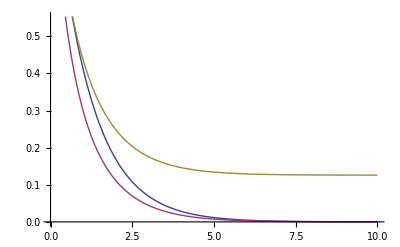

```mathematica
Plot[{ⅇ^(-t Gamma[π/2]),(ⅇ^(-t Gamma[π/2]-t Gamma[π]) (-2 ⅇ^(t Gamma[π/2]) Gamma[π/2]+ⅇ^(t Gamma[π]) Gamma[π/2]+ⅇ^(t Gamma[π/2]) Gamma[π]))/(-Gamma[π/2]+Gamma[π]),(ⅇ^(-t Gamma[π/2]-t Gamma[π]) (2 ⅇ^(t Gamma[π/2]) Gamma[π/2]-2 ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π/2]-ⅇ^(t Gamma[π/2]) Gamma[π]-ⅇ^(t Gamma[π]) Gamma[π]+2 ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π]+ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π/2] Gamma[π]-ⅇ^(t Gamma[π/2]+t Gamma[π]) Gamma[π]^2))/((Gamma[π/2]-Gamma[π]) Gamma[π])},{t,0,10}]
```

```mathematica
k[n_]=Sinh[n]
```

Sinh[n]

```mathematica
DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==1,x3[0]==1},{x1[t],x2[t],x3[t]},t]
```

{{x1[t]→ⅇ^(-t Sinh[1]),x2[t]→(ⅇ^(-t Sinh[1]-t Sinh[2]) (-2 ⅇ^(t Sinh[1]) Sinh[1]+ⅇ^(t Sinh[2]) Sinh[1]+ⅇ^(t Sinh[1]) Sinh[2]))/(-Sinh[1]+Sinh[2]),x3[t]→-1/(-Sinh[1]+Sinh[2])ⅇ^(-t Sinh[1]-t Sinh[2]) (-ⅇ^(t Sinh[1])-ⅇ^(t Sinh[2])+2 ⅇ^(t Sinh[1]+t Sinh[2])+ⅇ^(t Sinh[1]+t Sinh[2]) Sinh[1]+2 ⅇ^(t Sinh[1]) Csch[2] Sinh[1]-2 ⅇ^(t Sinh[1]+t Sinh[2]) Csch[2] Sinh[1]-ⅇ^(t Sinh[1]+t Sinh[2]) Sinh[2])}}

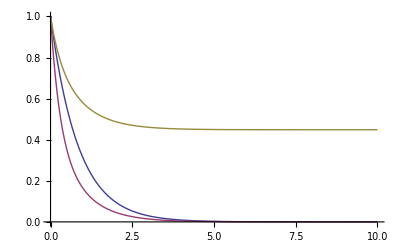

```mathematica
Plot[{ⅇ^(-t Sinh[1]),(ⅇ^(-t Sinh[1]-t Sinh[2]) (-2 ⅇ^(t Sinh[1]) Sinh[1]+ⅇ^(t Sinh[2]) Sinh[1]+ⅇ^(t Sinh[1]) Sinh[2]))/(-Sinh[1]+Sinh[2]),-1/(-Sinh[1]+Sinh[2])ⅇ^(-t Sinh[1]-t Sinh[2]) (-ⅇ^(t Sinh[1])-ⅇ^(t Sinh[2])+2 ⅇ^(t Sinh[1]+t Sinh[2])+ⅇ^(t Sinh[1]+t Sinh[2]) Sinh[1]+2 ⅇ^(t Sinh[1]) Csch[2] Sinh[1]-2 ⅇ^(t Sinh[1]+t Sinh[2]) Csch[2] Sinh[1]-ⅇ^(t Sinh[1]+t Sinh[2]) Sinh[2])},{t,0,10}]
```

```mathematica
k[n_]=Erf[n]
```

Erf[n]

```mathematica
DSolve[{x1'[t] == -k[1]*x1[t],x2'[t] ==k[1]*x1[t]-k[2]*x2[t],x3'[t] == -x2[t],x1[0]==1,x2[0]==1,x3[0]==1},{x1[t],x2[t],x3[t]},t]
```

{{x1[t]→ⅇ^(-t Erf[1]),x2[t]→(ⅇ^(-t Erf[1]-t Erf[2]) (-2 ⅇ^(t Erf[1]) Erf[1]+ⅇ^(t Erf[2]) Erf[1]+ⅇ^(t Erf[1]) Erf[2]))/(-Erf[1]+Erf[2]),x3[t]→(ⅇ^(-t Erf[1]-t Erf[2]) (-2 ⅇ^(t Erf[1]) Erf[1]+2 ⅇ^(t Erf[1]+t Erf[2]) Erf[1]+ⅇ^(t Erf[1]) Erf[2]+ⅇ^(t Erf[2]) Erf[2]-2 ⅇ^(t Erf[1]+t Erf[2]) Erf[2]-ⅇ^(t Erf[1]+t Erf[2]) Erf[1] Erf[2]+ⅇ^(t Erf[1]+t Erf[2]) Erf[2]^2))/(Erf[2] (-Erf[1]+Erf[2]))}}

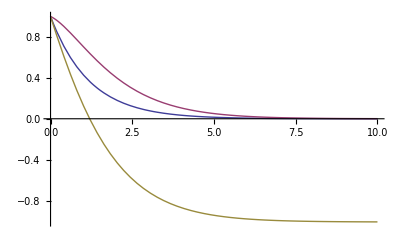

```mathematica
Plot[{ⅇ^(-t Erf[1]),(ⅇ^(-t Erf[1]-t Erf[2]) (-2 ⅇ^(t Erf[1]) Erf[1]+ⅇ^(t Erf[2]) Erf[1]+ⅇ^(t Erf[1]) Erf[2]))/(-Erf[1]+Erf[2]),(ⅇ^(-t Erf[1]-t Erf[2]) (-2 ⅇ^(t Erf[1]) Erf[1]+2 ⅇ^(t Erf[1]+t Erf[2]) Erf[1]+ⅇ^(t Erf[1]) Erf[2]+ⅇ^(t Erf[2]) Erf[2]-2 ⅇ^(t Erf[1]+t Erf[2]) Erf[2]-ⅇ^(t Erf[1]+t Erf[2]) Erf[1] Erf[2]+ⅇ^(t Erf[1]+t Erf[2]) Erf[2]^2))/(Erf[2] (-Erf[1]+Erf[2]))},{t,0,10}]
```

```mathematica
It is possible to study other dependencies of k on n rather simply in Mathematica.  k[n] could depend on n as an exponential, logarithm, tangent, cosh, besselJ,besselY,complimentary erf, etc.).
```

```mathematica
Alternatively, the system could be defined as a recursive, such as:
```

```mathematica
x[n+1,t]=x[n]*k[n]-k[n+1]*x[n+1]
```

```mathematica
with k[0]=0 and x[0,t]=0.
```

```mathematica
I haven't completely worked the recursive formulation out yet.  However, once the system is diagnalized, then the solution to a certain differential equation is determined by the initial condition of the last step in the reaction. Generally, in reactor design the initial condition of the reactant is specified.
```

```mathematica
In this case, the general form is:
```

```mathematica
({{x1[t]}, {x2[t]}, {x3[t]}})=A*Exp[λ1*t]+B*Exp[λ1*t]+...
```

```mathematica
where λ1 and λ2 are the first and second eigenvalues
```

```mathematica
For the 3by3 case
```

```mathematica
{{-k1, 0, 0}, {k1, -k2, 0}, {0, k2, -k3}}
```

```mathematica
Eigenvalues[{{-k1, 0, 0}, {k1, -k2, 0}, {0, k2, -k3}}]
```

{-k1,-k2,-k3}

```mathematica
MatrixForm[Eigenvectors[{{-k1, 0, 0}, {k1, -k2, 0}, {0, k2, -k3}}]]
```

(((k1-k2) (k1-k3))/(k1 k2) | -(k1-k3)/k2 | 1
0 | -(k2-k3)/k2 | 1
0 | 0 | 1)

```mathematica
MatrixForm[Eigenvectors[{{-k1, 0, 0}, {k1, -k2, 0}, {0, k2, -k3}}].({{-k1, 0, 0}, {k1, -k2, 0}, {0, k2, -k3}}).Inverse[Eigenvectors[{{-k1, 0, 0}, {k1, -k2, 0}, {0, k2, -k3}}]]]
```

((k1 (1-k1/k2) k2^2 k3)/((k1-k2) (k1-k3) (k2-k3))-(k1 k2^2 (k1+k2-k3) (k1/k2-k3/k2))/((k1-k2) (k1-k3) (k2-k3))-(k1 k2^2 (-(k1 (k1-k3))/k2-((k1-k2) (k1-k3))/k2) (-1+k3/k2))/((k1-k2) (k1-k3) (k2-k3)) | -(k1 k2^2 (k1+k2-k3) (-1+k1/k2+k3/k1-k3/k2))/((k1-k2) (k1-k3) (k2-k3))+(k1 k2^2 k3 (1-k1/k2-k3/k1+k3/k2))/((k1-k2) (k1-k3) (k2-k3)) | -k3
(k1 (1-k1/k2) k2^2 k3)/((k1-k2) (k1-k3) (k2-k3))-(k1 k2^2 (2 k2-k3) (k1/k2-k3/k2))/((k1-k2) (k1-k3) (k2-k3))+(k1^2 k2 (-1+k3/k2))/((k1-k2) (k1-k3)) | -(k1 k2^2 (2 k2-k3) (-1+k1/k2+k3/k1-k3/k2))/((k1-k2) (k1-k3) (k2-k3))+(k1 k2^2 k3 (1-k1/k2-k3/k1+k3/k2))/((k1-k2) (k1-k3) (k2-k3)) | -k3
(k1 (1-k1/k2) k2^2 k3)/((k1-k2) (k1-k3) (k2-k3))-(k1 k2^3 (k1/k2-k3/k2))/((k1-k2) (k1-k3) (k2-k3)) | -(k1 k2^3 (-1+k1/k2+k3/k1-k3/k2))/((k1-k2) (k1-k3) (k2-k3))+(k1 k2^2 k3 (1-k1/k2-k3/k1+k3/k2))/((k1-k2) (k1-k3) (k2-k3)) | -k3)

```mathematica
Note, the transpose can be dropped for using the inverse of the eigenvalues on the left hand side and the matrix of eigenvalues on the right hand side (instead of the reverse of this as was defined in class).
```

```mathematica
For the 4by4 case:
```

```mathematica
{{-k1, 0, 0, 0}, {k1, -k2, 0, 0}, {0, k2, -k3, 0}, {0, 0, k3, k4}}
```

```mathematica
Eigenvalues[{{-k1, 0, 0, 0}, {k1, -k2, 0, 0}, {0, k2, -k3, 0}, {0, 0, k3, k4}}]
```

{-k1,-k2,-k3,k4}

```mathematica
MatrixForm[Eigenvectors[{{-k1, 0, 0, 0}, {k1, -k2, 0, 0}, {0, k2, -k3, 0}, {0, 0, k3, k4}}]]
```

(-((k1-k2) (k1-k3) (k1+k4))/(k1 k2 k3) | ((k1-k3) (k1+k4))/(k2 k3) | -(k1+k4)/k3 | 1
0 | ((k2-k3) (k2+k4))/(k2 k3) | -(k2+k4)/k3 | 1
0 | 0 | -(k3+k4)/k3 | 1
0 | 0 | 0 | 1)

```mathematica
{{-k1, 0, 0, 0, 0}, {k1, -k2, 0, 0, 0}, {0, k2, -k3, 0, 0}, {0, 0, k3, -k4, 0}, {0, 0, 0, k4, -k5}}
```

```mathematica
Eigenvalues[{{-k1, 0, 0, 0, 0}, {k1, -k2, 0, 0, 0}, {0, k2, -k3, 0, 0}, {0, 0, k3, -k4, 0}, {0, 0, 0, k4, -k5}}]
```

{-k1,-k2,-k3,-k4,-k5}

```mathematica
MatrixForm[Eigenvectors[{{-k1, 0, 0, 0, 0}, {k1, -k2, 0, 0, 0}, {0, k2, -k3, 0, 0}, {0, 0, k3, -k4, 0}, {0, 0, 0, k4, -k5}}]]
```

(((k1-k2) (k1-k3) (k1-k4) (k1-k5))/(k1 k2 k3 k4) | -((k1-k3) (k1-k4) (k1-k5))/(k2 k3 k4) | ((k1-k4) (k1-k5))/(k3 k4) | -(k1-k5)/k4 | 1
0 | -((k2-k3) (k2-k4) (k2-k5))/(k2 k3 k4) | ((k2-k4) (k2-k5))/(k3 k4) | -(k2-k5)/k4 | 1
0 | 0 | ((k3-k4) (k3-k5))/(k3 k4) | -(k3-k5)/k4 | 1
0 | 0 | 0 | -(k4-k5)/k4 | 1
0 | 0 | 0 | 0 | 1)

```mathematica
Future consideration: Is there a way to generate arbitrary sized matrices of this form?
```

```mathematica
T.A.T^-1
```

```mathematica
Part B: To solve differential equations with matrices, we must find the eigenvalues and eigenvectors.  These will correspond to the solutions when the general form of the differential equation is assumed.  The Diagonalization process is helpful because it picks out the eigenvalues as the entries along the main diagonal. As it turns out, the matrix starts in a lower diagnalized form, for which the eigenvalues are also along the main diagonal.  This is somewhat circular because the eigenvectors will assist in the diagnalization of the rate constant matrix.  Typically in hand computations the eigenvalues are found first.  With Mathematica, the ordering of these processes is not mandatory.  The eigenvalues and eigenvectors are substituted into the general form of the system, which can be fairly complex, but is not in this case.  Then the solutions to the equations can be understood simultaneously. It is interesting to see the relationship between the exponent of the eigenvalue matrix as defined in problem 2 and it coming up again in Problem 3 for this form of the differential equation.
Also, my efforts indicate that the rotation matrix is not diagnalizable in the 2D case.
```

```mathematica
Clear[k]
```

```mathematica
Part C:
```

```mathematica
k[n_]=1
```

1

```mathematica
{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}
```

{{-1,0,0},{1,-1,0},{0,1,-1}}

```mathematica
Eigenvalues[{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}]
```

{-1,-1,-1}

```mathematica
Eigenvectors[{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}]
```

{{0,0,1},{0,0,0},{0,0,0}}

```mathematica
{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}
```

{{-1,0,0,0},{1,-1,0,0},{0,1,-1,0},{0,0,1,-1}}

```mathematica
Eigenvalues[{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}]
```

{-1,-1,-1,-1}

```mathematica
Eigenvectors[{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}]
```

{{0,0,0,1},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}
```

{{-1,0,0,0,0},{1,-1,0,0,0},{0,1,-1,0,0},{0,0,1,-1,0},{0,0,0,1,-1}}

```mathematica
Eigenvalues[{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}]
```

{-1,-1,-1,-1,-1}

```mathematica
Eigenvectors[{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}]
```

{{0,0,0,0,1},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
Part C:
```

```mathematica
k[n_]=Sin[n*Pi/2]
```

Sin[(n π)/2]

```mathematica
{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}
```

{{-1,0,0},{1,0,0},{0,0,1}}

```mathematica
Eigenvalues[{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}]
```

{-1,1,0}

```mathematica
Eigenvectors[{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}]
```

{{-1,1,0},{0,0,1},{0,1,0}}

```mathematica
{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}
```

{{-1,0,0,0},{1,0,0,0},{0,0,1,0},{0,0,-1,0}}

```mathematica
Eigenvalues[{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}]
```

{-1,1,0,0}

```mathematica
Eigenvectors[{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}]
```

{{-1,1,0,0},{0,0,-1,1},{0,0,0,1},{0,1,0,0}}

```mathematica
{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}
```

{{-1,0,0,0,0},{1,0,0,0,0},{0,0,1,0,0},{0,0,-1,0,0},{0,0,0,0,-1}}

```mathematica
Eigenvalues[{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}]
```

{-1,-1,1,0,0}

```mathematica
Eigenvectors[{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}]
```

{{0,0,0,0,1},{-1,1,0,0,0},{0,0,-1,1,0},{0,0,0,1,0},{0,1,0,0,0}}

```mathematica
k[n_]=InverseErf[n/(n+1)]
```

InverseErf[n/(1+n)]

```mathematica
{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}
```

{{-InverseErf[1/2],0,0},{InverseErf[1/2],-InverseErf[2/3],0},{0,InverseErf[2/3],-InverseErf[3/4]}}

```mathematica
Eigenvalues[{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}]
```

{-InverseErf[3/4],-InverseErf[2/3],-InverseErf[1/2]}

```mathematica
Eigenvectors[{{-k[1], 0, 0}, {k[1], -k[2], 0}, {0, k[2], -k[3]}}]
```

{{0,0,1},{0,-(InverseErf[2/3]-InverseErf[3/4])/InverseErf[2/3],1},{((InverseErf[1/2]-InverseErf[2/3]) (InverseErf[1/2]-InverseErf[3/4]))/(InverseErf[1/2] InverseErf[2/3]),-(InverseErf[1/2]-InverseErf[3/4])/InverseErf[2/3],1}}

```mathematica
{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}
```

{{-InverseErf[1/2],0,0,0},{InverseErf[1/2],-InverseErf[2/3],0,0},{0,InverseErf[2/3],-InverseErf[3/4],0},{0,0,InverseErf[3/4],-InverseErf[4/5]}}

```mathematica
Eigenvalues[{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}]
```

{-InverseErf[4/5],-InverseErf[3/4],-InverseErf[2/3],-InverseErf[1/2]}

```mathematica
Eigenvectors[{{-k[1], 0, 0, 0}, {k[1], -k[2], 0, 0}, {0, k[2], -k[3], 0}, {0, 0, k[3], -k[4]}}]
```

{{0,0,0,1},{0,0,-(InverseErf[3/4]-InverseErf[4/5])/InverseErf[3/4],1},{0,((InverseErf[2/3]-InverseErf[3/4]) (InverseErf[2/3]-InverseErf[4/5]))/(InverseErf[2/3] InverseErf[3/4]),-(InverseErf[2/3]-InverseErf[4/5])/InverseErf[3/4],1},{-((InverseErf[1/2]-InverseErf[2/3]) (InverseErf[1/2]-InverseErf[3/4]) (InverseErf[1/2]-InverseErf[4/5]))/(InverseErf[1/2] InverseErf[2/3] InverseErf[3/4]),((InverseErf[1/2]-InverseErf[3/4]) (InverseErf[1/2]-InverseErf[4/5]))/(InverseErf[2/3] InverseErf[3/4]),-(InverseErf[1/2]-InverseErf[4/5])/InverseErf[3/4],1}}

```mathematica
{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}
```

{{-InverseErf[1/2],0,0,0,0},{InverseErf[1/2],-InverseErf[2/3],0,0,0},{0,InverseErf[2/3],-InverseErf[3/4],0,0},{0,0,InverseErf[3/4],-InverseErf[4/5],0},{0,0,0,InverseErf[4/5],-InverseErf[5/6]}}

```mathematica
Eigenvalues[{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}]
```

{-InverseErf[5/6],-InverseErf[4/5],-InverseErf[3/4],-InverseErf[2/3],-InverseErf[1/2]}

```mathematica
Eigenvectors[{{-k[1], 0, 0, 0, 0}, {k[1], -k[2], 0, 0, 0}, {0, k[2], -k[3], 0, 0}, {0, 0, k[3], -k[4], 0}, {0, 0, 0, k[4], -k[5]}}]
```

{{0,0,0,0,1},{0,0,0,-(InverseErf[4/5]-InverseErf[5/6])/InverseErf[4/5],1},{0,0,((InverseErf[3/4]-InverseErf[4/5]) (InverseErf[3/4]-InverseErf[5/6]))/(InverseErf[3/4] InverseErf[4/5]),-(InverseErf[3/4]-InverseErf[5/6])/InverseErf[4/5],1},{0,-((InverseErf[2/3]-InverseErf[3/4]) (InverseErf[2/3]-InverseErf[4/5]) (InverseErf[2/3]-InverseErf[5/6]))/(InverseErf[2/3] InverseErf[3/4] InverseErf[4/5]),((InverseErf[2/3]-InverseErf[4/5]) (InverseErf[2/3]-InverseErf[5/6]))/(InverseErf[3/4] InverseErf[4/5]),-(InverseErf[2/3]-InverseErf[5/6])/InverseErf[4/5],1},{((InverseErf[1/2]-InverseErf[2/3]) (InverseErf[1/2]-InverseErf[3/4]) (InverseErf[1/2]-InverseErf[4/5]) (InverseErf[1/2]-InverseErf[5/6]))/(InverseErf[1/2] InverseErf[2/3] InverseErf[3/4] InverseErf[4/5]),-((InverseErf[1/2]-InverseErf[3/4]) (InverseErf[1/2]-InverseErf[4/5]) (InverseErf[1/2]-InverseErf[5/6]))/(InverseErf[2/3] InverseErf[3/4] InverseErf[4/5]),((InverseErf[1/2]-InverseErf[4/5]) (InverseErf[1/2]-InverseErf[5/6]))/(InverseErf[3/4] InverseErf[4/5]),-(InverseErf[1/2]-InverseErf[5/6])/InverseErf[4/5],1}}

```mathematica
Things to work on in the future regarding this assignment:
```

```mathematica
-Logic operations on Matrices in Mathematica
```

```mathematica
Originals:
```

```mathematica
fib[n_]:=Module[{f},f[1]=f[2]=1;
f[i_]:=f[i]=f[i-1]+f[i-2];
f[n]]
```

```mathematica
fib[5]
```

```mathematica
The trick to doing the infinite product is also in the Module command:
```

```mathematica
gcd[m0_,n0_]:=Module[{m=m0,n=n0},While[n≠0,{m,n}={n,Mod[m,n]}];
m]
```

```mathematica
gcd[18,21]
```

```mathematica
Modified:
```

```mathematica
fib[n_]:=Module[{f},{For[n>1,f[n,0]=0};
f[i_]:=f[i]=f[i-1]+f[i-2];
f[n]]
```